Άσκηση 6.3

Στο σύστημα Ήλιος-Δίας (μ=0.001) θεωρούμε αστεροειδή που (χωρίς τη διαταραχή του Δία) κινείται σε έλλειψη με εκκεντρότητα e=0.3 και περίοδο διπλάσια αυτής του Δία. Βρείτε τις αρχικές συνθήκες του αστεροειδή για τις περιπτώσεις που ο αστεροειδής βρίσκεται για t=0 στο περίκεντρο ή στο απόκεντρο της ελλειπτικής τροχιάς.

Για αυτές τις αρχικές συνθηκες ολοκληρώστε τις εξισώσεις RTBP και σχεδιάστε την χρονική εξέλιξη του μεγάλου ημιάξονα και της εκκεντρότητας της τροχιάς του αστεροειδή.

Λύση

```mathematica
ClearAll["Global`*"]
μ=0.001;e0=0.3;T=4π;(* m0 = G M *)m0=1-μ;ω=(2π)/T;
```

Για τον αστεροειδή έχουμε T=2π √(a^3/m_0), επομένως

```mathematica
StringForm["a = ``",a=((m0 T)/(4 π^2))^(1/3)]
```

a = 0.682556

Από την εκκεντρότητα και τον μεγάλο ημιάξονα υπολογίζουμε τις αποστάσεις του περικέντρου και αποκέντρου.

```mathematica
StringForm["r_min = ``",rmin=a(1-e0)]
StringForm["r_max = ``",rmax=a(1+e0)]
```

r_min = 0.477789

r_max = 0.887323

Ορίζουμε την βοηθητική συνάρτηση που μετατρέπει τις καρτεσιανές θέσεις και ταχύτητες του αστεροειδή σε στοιχεία τροχιάς Kepler.

```mathematica
CartesianToKepler3D[r_List,u_List,t_,μ_:1]:=Module[
{
c,h,a,e,i,Ω,cosΩ,sinΩ,ω,cosωf,sinωf,M,cosE,sinE,EE,f,cosf,sinf,n,angle,T,τ
},
(* υπολογίζουμε την ενέργεια και την στροφορμή *)
c=1/2 Norm[u]^2-μ/Norm[r];h=Cross[r,u];
(* διακόπτουμε τη ροή αν η ενέργεια βγει θετική - μας ενδιαφέρουν μόνο οι κλειστές τροχιές *)
If[c>0,Return[Style["Θετική ενέργεια --- Η τροχιά δεν είναι δέσμια.",{Red,Italic}]]];
(* υπολογίζουμε τα στοιχεία της τροχιάς *)
	(* μεγάλος ημιάξονας *)a=-μ/(2c);
	(* εκκεντρότητα *)e=√(1+(2c Norm[h]^2)/μ^2);
	(* κλίση της τροχιάς *)i=ArcCos[h[[3]]/Norm[h]];
	(* μήκος του αναβιβάζοντος δεσμού *)sinΩ=Sign[h[[3]]] h[[1]]/(Norm[h]Sin[i]);cosΩ=-Sign[h[[3]]] h[[2]]/(Norm[h]Sin[i]);Ω=Mod[#,2π]&[ArcTan[cosΩ,sinΩ]];
	(* Ε *)cosE=(a-Norm[r])/(a e)sinE=(r.u)/(e √(μ a))EE=Mod[#,2π]&[ArcTan[cosE,sinE]];
	(* n *)n=μ^(1/2)a^(-3/2);
	(* μέση ανωμαλία   M=E-e sinE *)M=EE-e sinE;
	(* αληθής ανωμαλία f *)cosf=(cosE-e)/(1-e cosE)sinf=(√(1-e^2)sinE)/(1-e cosE)f=Mod[#,2π]&[ArcTan[cosf,sinf]];
	(* γωνία περικέντρου ω *)cosωf=(r[[1]] cosΩ+r[[2]]sinΩ)/Norm[r];sinωf=r[[3]]/(Norm[r] Sin[i]);ω=Mod[#,2π]&[ArcTan[cosωf,sinωf]-f];
	(* περίοδος *)T=2π √(a^3/μ);
	(* τ *)τ=t-M/n;
(* επιστρέφουμε τα αποτελέσματα *)Association["a"->a,"e"->e,"i"->i,"Ω"->Ω,"ω"->ω,"M"->M,"τ"->τ,"T"->T,"n"->n]
]
e[ttt_]:=Quiet@CartesianToKepler3D[{XX/.t->ttt,YY/.t->ttt,0},{UX/.t->ttt,UY/.t->ttt,0},ttt]["e"];
```

Α Περίπτωση

Θεωρούμε ότι το περίκεντρο και το απόκεντρο βρίσκονται πάνω στην ευθεία που ενώνει τον Ήλιο με τον Δία κατά την αρχική στιγμή.

Η αρχική θέση του δορυφόρου θα είναι σε κάθε περίπτωση η:

```mathematica
StringForm["Περίκεντρο: r_περ = (-``, 0)",rmin]
StringForm["Απόκεντρο: r_απ = (``, 0)",rmax]
```

Περίκεντρο: r_περ = (-0.477789, 0)

Απόκεντρο: r_απ = (0.887323, 0)

Η ενέργεια του δορυφόρου υπολογίζεται πάλι απ’ τον μεγάλο ημιάξονα: a=-m_0/(2 C)

```mathematica
StringForm["C = ``",c=-m0/(2a)]
```

C = -0.731808

Στο περίκεντρο και στο απόκεντρο η ταχύτητα του αστεροειδή έχει μόνο y συνιστώσα. Επομένως, την υπολογίζουμε από την ενέργεια: C=1/2 u^2-m_0/(|r|)

```mathematica
StringForm["Περίκεντρο: u_περ = (0, ``)",uper=√(2c+(2m0)/rmin)]
StringForm["Απόκεντρο: u_απ = (0, ``)",uap=√(2c+(2m0)/rmax)]
```

Περίκεντρο: u_περ = (0, 1.64868)

Απόκεντρο: u_απ = (0, 0.88775)

Οι εξισώσεις του RTBP είναι οι παρακάτω:

```mathematica
r1[t]=√((x[t]+μ)^2+y[t]^2);r2[t]=√((x[t]-1+μ)^2+y[t]^2);
deq1=x''[t]==2y'[t]+x[t]-(1-μ)(x[t]+μ)/r1[t]^3-μ(x[t]-(1-μ))/r2[t]^3;
deq2=y''[t]==-2x'[t]+y[t]-(1-μ)y[t]/r1[t]^3-μ y[t]/r2[t]^3;
```

Ορίζουμε το πρόβλημα των αρχικών συνθηκών, για την κάθε περίπτωση, και το λύνουμε. Έπειτα, διαμερίζουμε το διάστημα του χρόνου (0, t_max) και για κάθε στιγμή υπολογίζουμε την εκκεντρότητα της τροχιάς με βάση την αντίστοιχη θέση και ταχύτητα του αστεροειδή (με τη βοήθεια της συνάρτησης CartesianToKepler).

Αρχική θέση στο περίκεντρο, ο δορυφόρος κινείται σε φάση με τον Δία

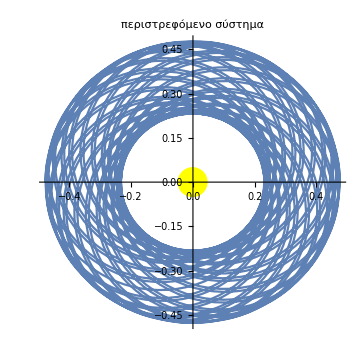
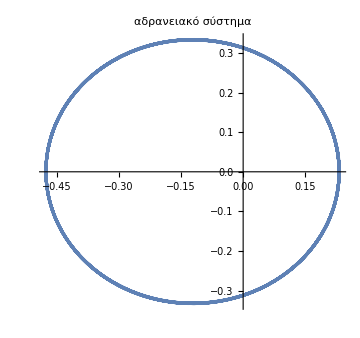
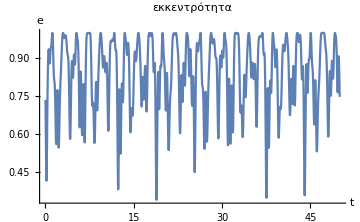
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==-rmin,y[0]==0,x'[0]==0,y'[0]==uper};
tmax=50;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής παραμένει σε τροχιά που περιορίζεται σε δακτύλιο μεταξύ Ήλιου και Δία.

Αρχική θέση στο περίκεντρο, ο δορυφόρος κινείται σε αντίθετη φάση με τον Δία

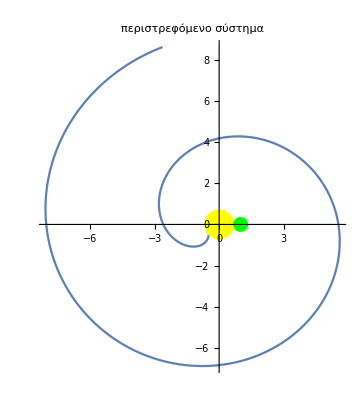
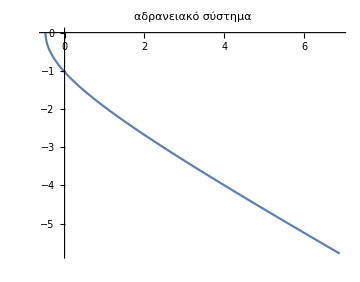
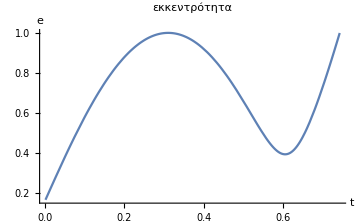
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==-rmin,y[0]==0,x'[0]==0,y'[0]==-uper};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"},PlotRange->All];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει στο άπειρο.

Αρχική θέση στο απόκεντρο, ο δορυφόρος κινείται σε φάση με τον Δία

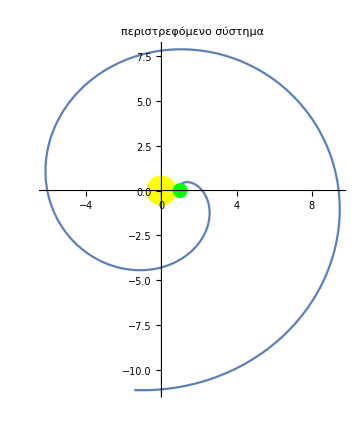
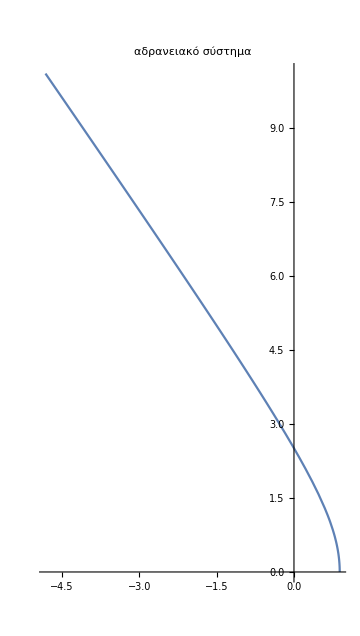
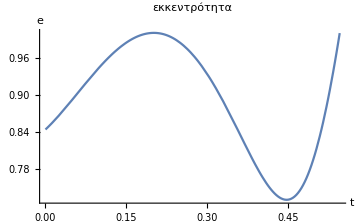
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==rmax,y[0]==0,x'[0]==0,y'[0]==uap};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"},PlotRange->All];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει στο άπειρο.

Αρχική θέση στο απόκεντρο, ο δορυφόρος κινείται σε αντίθετη φάση με τον Δία

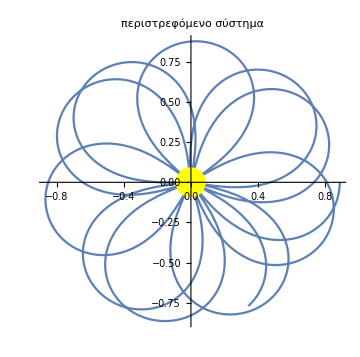
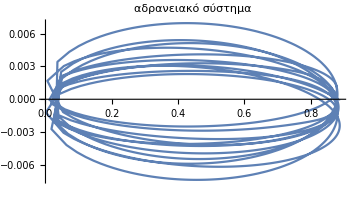
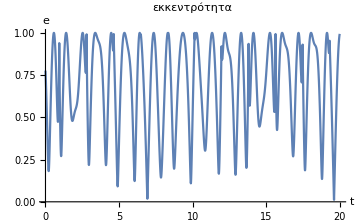
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==rmax,y[0]==0,x'[0]==0,y'[0]==-uap};
tmax=20;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"},PlotRange->All];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Φαίνεται ότι ο αστεροειδής προσκρούει στον Ήλιο.

Β Περίπτωση

Θεωρούμε ότι το περίκεντρο και το απόκεντρο βρίσκονται πάνω σε ευθεία κάθετη σ’ αυτήν που ενώνει τον Ήλιο με τον Δία κατά την αρχική στιγμή, με το περίκεντρο στα θετικά y.

Η αρχική θέση του δορυφόρου θα είναι σε κάθε περίπτωση η:

```mathematica
StringForm["Περίκεντρο: r_περ = (0, ``)",rmin]
StringForm["Απόκεντρο: r_απ = (, -``)",rmax]
```

Περίκεντρο: r_περ = (0, 0.477789)

Απόκεντρο: r_απ = (, -0.887323)

Η ενέργεια του δορυφόρου υπολογίζεται πάλι απ’ τον μεγάλο ημιάξονα: a=-m_0/(2 C)

```mathematica
StringForm["C = ``",c=-m0/(2a)]
```

C = -0.731808

Στο περίκεντρο και στο απόκεντρο η ταχύτητα του αστεροειδή έχει μόνο y συνιστώσα. Επομένως, την υπολογίζουμε από την ενέργεια: C=1/2 u^2-m_0/(|r|)

```mathematica
StringForm["Περίκεντρο: u_περ = (``, 0)",uper=√(2c+(2m0)/rmin)]
StringForm["Απόκεντρο: u_απ = (``, 0)",uap=√(2c+(2m0)/rmax)]
```

Περίκεντρο: u_περ = (1.64868, 0)

Απόκεντρο: u_απ = (0.88775, 0)

Οι εξισώσεις του RTBP είναι οι παρακάτω:

```mathematica
r1[t]=√((x[t]+μ)^2+y[t]^2);r2[t]=√((x[t]-1+μ)^2+y[t]^2);
deq1=x''[t]==2y'[t]+x[t]-(1-μ)(x[t]+μ)/r1[t]^3-μ(x[t]-(1-μ))/r2[t]^3;
deq2=y''[t]==-2x'[t]+y[t]-(1-μ)y[t]/r1[t]^3-μ y[t]/r2[t]^3;
```

Ορίζουμε το πρόβλημα των αρχικών συνθηκών, για την κάθε περίπτωση, και το λύνουμε. Έπειτα, διαμερίζουμε το διάστημα του χρόνου (0, t_max) και για κάθε στιγμή υπολογίζουμε την εκκεντρότητα της τροχιάς με βάση την αντίστοιχη θέση και ταχύτητα του αστεροειδή (με τη βοήθεια της συνάρτησης CartesianToKepler).

Αρχική θέση στο περίκεντρο, ο δορυφόρος κινείται σε φάση με τον Δία

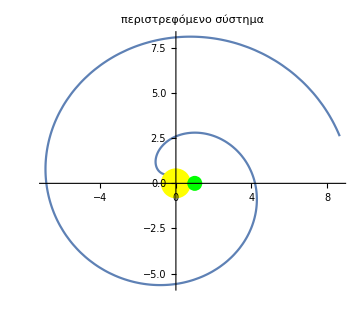
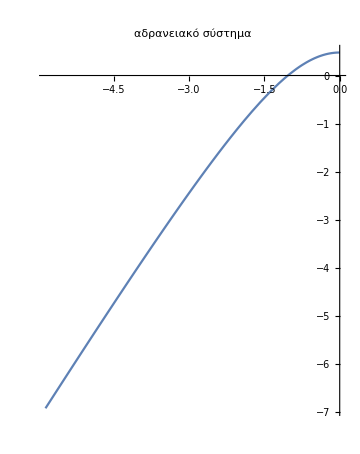
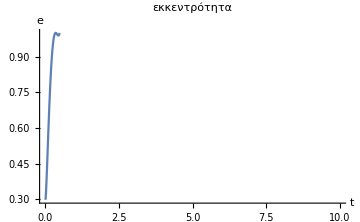
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==0,y[0]==rmin,x'[0]==-uper,y'[0]==0};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει από το σύστημα.

Αρχική θέση στο περίκεντρο, ο δορυφόρος κινείται σε αντίθετη φάση με τον Δία

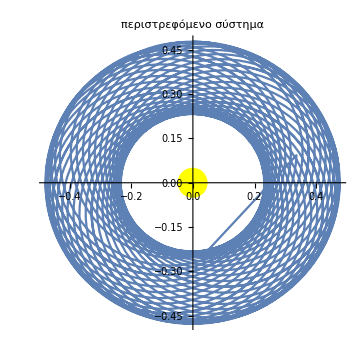
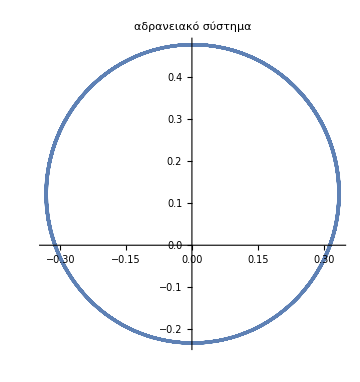
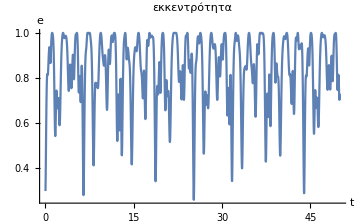
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==0,y[0]==rmin,x'[0]==uper,y'[0]==0};
tmax=50;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής κινείται μέσα σε δακτύλιο, στην περιοχή ανάμεσα σε Ήλιο-Δία.

Αρχική θέση στο απόκεντρο, ο δορυφόρος κινείται σε φάση με τον Δία

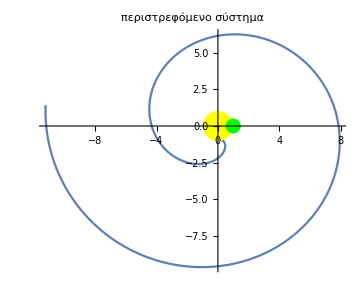
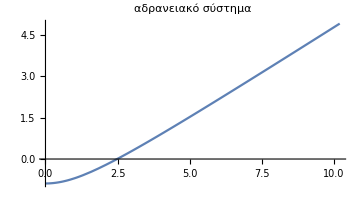
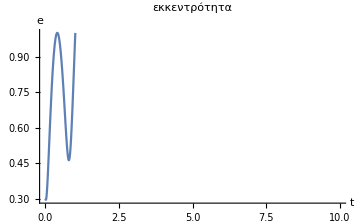
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==0,y[0]==-rmax,x'[0]==uap,y'[0]==0};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει από το σύστημα.

Αρχική θέση στο απόκεντρο, ο δορυφόρος κινείται σε αντίθετη φάση με τον Δία

NDSolve::ndsz: At t == 0.92803, step size is effectively zero; singularity or stiff system suspected.

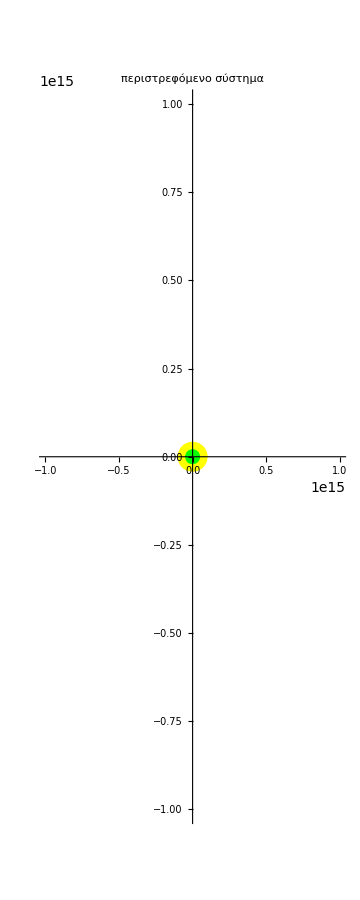
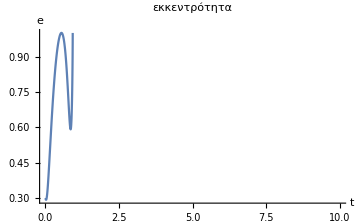
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==0,y[0]==-rmax,x'[0]==-uap,y'[0]==0};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει από το σύστημα.